```mathematica
Clear[interPP,isumPP ,isumZP,isumZZ,isumWW,isumWWdyt]
SetDirectory[NotebookDirectory[]];
interPP = Get["intang_PPtt_10TeV_fix.txt"];
interZP = Get["intang_ZPtt_10TeV_fix.txt"];
factor=0.3894*10^15;
```



```mathematica
(*benchmarklist={3,4,5,7,8,10,11};*)
ColorData[24,"Image"]
(*ColorData[109,"Image"]*)
colorselecitonumber=24;
```

```mathematica
energygrid=Grid[{Table[Style[If[j==1,{"(√s= 3,","6,","10,","14,","30,","100 TeV)"}[[i]],"TeV"],If[j≠0,ColorData[colorselecitonumber][i]],Bold],{j,1,2,1},{i,1,6,1}][[1]]},Spacings->{0.5,0}]
```

(√s= 3, | 6, | 10, | 14, | 30, | 100 TeV)

```mathematica
interWW = Get["intang_WWtt1.txt"];
interZZ = Get["intang_ZZtt_10TeV_Fix.txt"];
```

```mathematica
dytinterWW = Get["VLQ_ww00_10TeV.txt"];
dytinterWW01 = Get["VLQ_ww01_10TeV.txt"];
dytinterWW0m1 = Get["VLQ_ww0m1_10TeV.txt"];
dytinterWW10 = Get["VLQ_ww10_10TeV.txt"];
dytinterWWm10 = Get["VLQ_wwm10_10TeV.txt"];
dytinterWW11 = Get["VLQ_ww11_10TeV.txt"];
dytinterWWm1m1 = Get["VLQ_wwm1m1_10TeV.txt"];
dytinterWW1m1 = Get["VLQ_ww1m1_10TeV.txt"];
dytinterWWm11 = Get["VLQ_wwm11_10TeV.txt"];
dytt = Table[(1/20000)*(10i),{i,0,20}]
```

{0,1/2000,1/1000,3/2000,1/500,1/400,3/1000,7/2000,1/250,9/2000,1/200,11/2000,3/500,13/2000,7/1000,3/400,1/125,17/2000,9/1000,19/2000,1/100}

```mathematica
dytinterZZ= Get["VLQ_zz00_10TeV.txt"];
dytinterZZ01 = Get["VLQ_zz01_10TeV.txt"];
dytinterZZ0m1 = Get["VLQ_zz0m1_10TeV.txt"];
dytinterZZ10 = Get["VLQ_zz10_10TeV.txt"];
dytinterZZm10 = Get["VLQ_zzm10_10TeV.txt"];
dytinterZZ11 = Get["VLQ_zz11_10TeV.txt"];
dytinterZZm1m1 = Get["VLQ_zzm1m1_10TeV.txt"];
dytinterZZ1m1 = Get["VLQ_zz1m1_10TeV.txt"];
dytinterZZm11 = Get["VLQ_zzm11_10TeV.txt"];
```

```mathematica
dytinterZP01 = Get["VLQ_zp10_10TeV.txt"];
dytinterZP0m1 = Get["VLQ_zpm10_10TeV.txt"];
dytinterZP11 = Get["VLQ_zp11_10TeV.txt"];
dytinterZPm1m1 = Get["VLQ_zpm1m1_10TeV.txt"];
dytinterZP1m1 = Get["VLQ_zp1m1_10TeV.txt"];
dytinterZPm11 = Get["VLQ_zpm11_10TeV.txt"];
```

```mathematica
dytt[[6]]
```

1/400

```mathematica
lum = 10;
br = 88.89;
```

```mathematica
sqrtsbin = Table[350 + 50*i, {i,0,194}];
thetaList=Table[0+(Pi/18)*i,{i,0,18}];
```

```mathematica
angenPP[ang_,num_] :=interPP[[ang]] [(1 + ((num - 350)/50))]

angenZP[ang_,num_] :=interZP[[ang]] [(1 + ((num - 350)/50))]

angenWW[ang_,num_] :=interWW[[ang]][(1 + ((num - 350)/50))]

angenZZ[ang_,num_] :=interZZ[[ang]][(1 + ((num - 350)/50))]
```

```mathematica
ADD VLQ DYT
isumWWdyt[ang_,dyt_,energy_] :=factor*(dytinterWW[[ang,dyt]][(1 + ((energy - 350)/50))]-dytinterWW[[ang,1]][(1 + ((energy - 350)/50))])
isumWW01dyt[ang_,dyt_,energy_] :=factor*(dytinterWW01 [[ang,dyt]][(1 + ((energy - 350)/50))]-dytinterWW01 [[ang,1]][(1 + ((energy - 350)/50))])
isumWW0m1dyt[ang_,dyt_,energy_] :=factor*(dytinterWW0m1  [[ang,dyt]][(1 + ((energy - 350)/50))]-dytinterWW0m1  [[ang,1]][(1 + ((energy - 350)/50))])
isumWW10dyt[ang_,dyt_,energy_] :=factor*(dytinterWW10 [[ang,dyt]][(1 + ((energy - 350)/50))]-dytinterWW10 [[ang,1]][(1 + ((energy - 350)/50))])
isumWWm10dyt[ang_,dyt_,energy_] :=factor*(dytinterWWm10  [[ang,dyt]][(1 + ((energy - 350)/50))]-dytinterWWm10  [[ang,1]][(1 + ((energy - 350)/50))])
isumWW1m1dyt[ang_,dyt_,energy_] :=factor*(dytinterWW1m1 [[ang,dyt]][(1 + ((energy - 350)/50))]-dytinterWW1m1 [[ang,1]][(1 + ((energy - 350)/50))])
isumWWm11dyt[ang_,dyt_,energy_] :=factor*(dytinterWWm11  [[ang,dyt]][(1 + ((energy - 350)/50))]-dytinterWWm11  [[ang,1]][(1 + ((energy - 350)/50))])
isumWW11dyt[ang_,dyt_,energy_] :=factor*(dytinterWW11 [[ang,dyt]][(1 + ((energy - 350)/50))]-dytinterWW11 [[ang,1]][(1 + ((energy - 350)/50))])
isumWWm1m1dyt[ang_,dyt_,energy_] :=factor*(dytinterWWm1m1  [[ang,dyt]][(1 + ((energy - 350)/50))]-dytinterWWm1m1 [[ang,1]][(1 + ((energy - 350)/50))])
```

ADD DYT VLQ

```mathematica
isumZZdyt[ang_,dyt_,energy_] :=factor*(dytinterZZ[[ang,dyt]][(1 + ((energy - 350)/50))]-dytinterZZ[[ang,1]][(1 + ((energy - 350)/50))])
isumZZ01dyt[ang_,dyt_,energy_] :=factor*(dytinterZZ01 [[ang,dyt]][(1 + ((energy - 350)/50))]-dytinterZZ01 [[ang,1]][(1 + ((energy - 350)/50))])
isumZZ0m1dyt[ang_,dyt_,energy_] :=factor*(dytinterZZ0m1  [[ang,dyt]][(1 + ((energy - 350)/50))]-dytinterZZ0m1  [[ang,1]][(1 + ((energy - 350)/50))])
isumZZ10dyt[ang_,dyt_,energy_] :=factor*(dytinterZZ10 [[ang,dyt]][(1 + ((energy - 350)/50))]-dytinterZZ10 [[ang,1]][(1 + ((energy - 350)/50))])
isumZZm10dyt[ang_,dyt_,energy_] :=factor*(dytinterZZm10  [[ang,dyt]][(1 + ((energy - 350)/50))]-dytinterZZm10  [[ang,1]][(1 + ((energy - 350)/50))])
isumZZ1m1dyt[ang_,dyt_,energy_] :=factor*(dytinterZZ1m1 [[ang,dyt]][(1 + ((energy - 350)/50))]-dytinterZZ1m1 [[ang,1]][(1 + ((energy - 350)/50))])
isumZZm11dyt[ang_,dyt_,energy_] :=factor*(dytinterZZm11  [[ang,dyt]][(1 + ((energy - 350)/50))]-dytinterZZm11  [[ang,1]][(1 + ((energy - 350)/50))])
isumZZ11dyt[ang_,dyt_,energy_] :=factor*(dytinterZZ11 [[ang,dyt]][(1 + ((energy - 350)/50))]-dytinterZZ11 [[ang,1]][(1 + ((energy - 350)/50))])
isumZZm1m1dyt[ang_,dyt_,energy_] :=factor*(dytinterZZm1m1  [[ang,dyt]][(1 + ((energy - 350)/50))]-dytinterZZm1m1 [[ang,1]][(1 + ((energy - 350)/50))])
```

```mathematica
isumZP01dyt[ang_,dyt_,energy_] :=factor*(dytinterZP01 [[ang,dyt]][(1 + ((energy - 350)/50))]-dytinterZP01 [[ang,1]][(1 + ((energy - 350)/50))])
isumZP0m1dyt[ang_,dyt_,energy_] :=factor*(dytinterZP0m1  [[ang,dyt]][(1 + ((energy - 350)/50))]-dytinterZP0m1  [[ang,1]][(1 + ((energy - 350)/50))])
isumZP1m1dyt[ang_,dyt_,energy_] :=factor*(dytinterZP1m1 [[ang,dyt]][(1 + ((energy - 350)/50))]-dytinterZP1m1 [[ang,1]][(1 + ((energy - 350)/50))])
isumZPm11dyt[ang_,dyt_,energy_] :=factor*(dytinterZPm11  [[ang,dyt]][(1 + ((energy - 350)/50))]-dytinterZPm11  [[ang,1]][(1 + ((energy - 350)/50))])
isumZP11dyt[ang_,dyt_,energy_] :=factor*(dytinterZP11 [[ang,dyt]][(1 + ((energy - 350)/50))]-dytinterZP11 [[ang,1]][(1 + ((energy - 350)/50))])
isumZPm1m1dyt[ang_,dyt_,energy_] :=factor*(dytinterZPm1m1  [[ang,dyt]][(1 + ((energy - 350)/50))]-dytinterZPm1m1 [[ang,1]][(1 + ((energy - 350)/50))])
```

```mathematica
background = Table[NIntegrate[lum * br*(angenPP[k,ss]+angenWW[k,ss]+2 angenZP[k,ss]+angenZZ[k,ss]),{ss,sqrtsbin[[i]],sqrtsbin[[i+1]]}],{i,1,53},{k,1,18}];

ADD SIGNAL VLQ
```

ADD SIGNAL VLQ

```mathematica
signal = Table[NIntegrate[lum * br*(isumWWdyt[k,j,ss] + isumWW01dyt[k,j,ss] + isumWW0m1dyt[k,j,ss] + isumWW10dyt[k,j,ss] + isumWWm10dyt[k,j,ss]   + isumWW1m1dyt[k,j,ss] + isumWW1m1dyt[k,j,ss] +isumWW11dyt[k,j,ss] + isumWWm1m1dyt[k,j,ss]+isumZZdyt[k,j,ss] + isumZZ01dyt[k,j,ss] + isumZZ0m1dyt[k,j,ss] + isumZZ10dyt[k,j,ss] + isumZZm10dyt[k,j,ss]   + isumZZ1m1dyt[k,j,ss] + isumZZ1m1dyt[k,j,ss] +isumZZ11dyt[k,j,ss] + isumZZm1m1dyt[k,j,ss] + 2  isumZP01dyt[k,j,ss] +2  isumZP0m1dyt[k,j,ss]   + 2  isumZP1m1dyt[k,j,ss] + 2 isumZPm11dyt[k,j,ss] +2 isumZP11dyt[k,j,ss] +2 isumZPm1m1dyt[k,j,ss]),{ss,sqrtsbin[[i]],sqrtsbin[[i+1]]}],{i,1,53},{k,1,18},{j,1,Length@dytt}]
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

```mathematica
(*Sum angles*)
sumanglesbkg = Table[Sum[background[[i,n]],{n,2,17}],{i,1,53}];
sumanglessig = Table[Sum[signal[[i,n,j]],{n,2,17}],{i,1,53},{j,1,Length@dytt}];
```

```mathematica
sqrtsumanglesbkg =Sqrt[sumanglesbkg];
```

```mathematica
(*background1 = Table[NIntegrate[lum * br*(angenPP[k,ss]+angenWW[k,ss]+angenZP[k,ss]+angenZZ[k,ss]),{ss,3000,10000}],{k,2,17}];*)
```

```mathematica
(*signal1 = Table[NIntegrate[lum * br*(isumWWdyt[k,j,ss]),{ss,3000,10000}],{k,2,17},{j,1,Length@dytt}];*)
```

```mathematica
(*Sum angles*)
(*sumanglesbkg1 = Sum[background1[[n]],{n,2,17}];
sumanglessig1 = Table[Sum[signal1[[n,j]],{n,2,17}],{j,1,Length@dytt}];
sqrtsumanglesbkg1 =Sqrt[sumanglesbkg1];*)
```

```mathematica
chi2sumang = Table[Sum[(sumanglessig [[i,j]]/sqrtsumanglesbkg [[i]])^2,{i,1,53}],{j,1,Length@dytt}];
```

```mathematica
chi2sumang1 = Table[(sumanglessig1 [[j]]/sqrtsumanglesbkg1)^2,{j,1,Length@dytt}];
```

Part::partd: Part specification sumanglessig1⟦1⟧ is longer than depth of object.

Part::partd: Part specification sumanglessig1⟦2⟧ is longer than depth of object.

Part::partd: Part specification sumanglessig1⟦3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

```mathematica
chi = chi2sumang +chi2sumang1 ;
```

```mathematica
dytt = Table[(1/20000)*(1000i),{i,0,20}]
dytchi2en = Table[{dytt[[k]],chi[[k]]},{k,1,Length@dytt}];
intdytchi2en = Interpolation[dytchi2en ]
sig1= Table[{dytt[[k]],1},{k,1,Length@dytt}];
```

{0,1/20,1/10,3/20,1/5,1/4,3/10,7/20,2/5,9/20,1/2,11/20,3/5,13/20,7/10,3/4,4/5,17/20,9/10,19/20,1}

InterpolatingFunction[…]

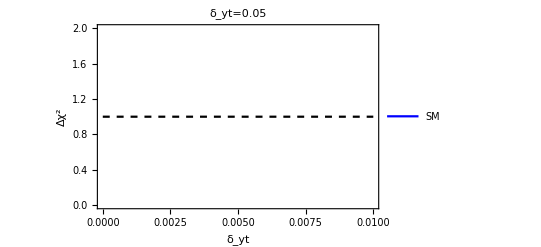

```mathematica
ListPlot[{intdytchi2en ,sig1},Joined->True,Frame->True,PlotStyle->{Blue,{Dashed,Black}},PlotLabel->Style["δ_yt=0.05",Black,20],PlotLegends->{"SM"},FrameLabel->{Style["δ_yt",Black,20],Style["Δχ^2",Black,15]},FrameTicksStyle->Directive[Black,13]]
```

```mathematica
(*bin angle and energy*)
sqrtback = Sqrt[background];
chi2 = Table[Sum[(signal[[i,j,k]]/ sqrtback[[i,j]])^2,{i,1,53},{j,2,17}],{k,1,Length@dytt}];
```

```mathematica
dytchi2enang = Table[{dytt[[k]],chi2 [[k]]},{k,1,Length@dytt}];
intdytchi2enang = Interpolation[dytchi2enang ];
 dyttnew = Table[(1/200000)*(1000i),{i,0,200}];
sig1= Table[{ dyttnew[[k]],1},{k,1,Length@ dyttnew}];
intsig1 = Interpolation[sig1 ]
```

InterpolatingFunction[…]

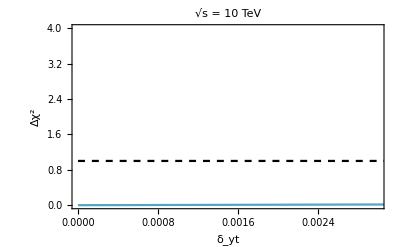

```mathematica
lineplot=ListPlot[{intdytchi2enang ,sig1},Joined->True,PlotStyle->{ColorData[colorselecitonumber][5],{Dashed,Black}},Frame->True,FrameLabel->{Style[DisplayForm["δ_yt"],Black,20,FontFamily->"Times"],Style["Δχ^2",Black,20,FontFamily->"Times"]},
PlotLabel->Style[DisplayForm[SqrtBox["s"] ]  Row[{" = ",10 TeV}]  ,Black,20,FontFamily->"Times"],
PlotRange->{{0,0.003},{0,4}},
FrameTicksStyle->Directive[Black,15],ImageSize->400]
```

```mathematica
Export["chi_square_10TeV_VLQ_dilepton_angle_out.pdf",lineplot]
```

chi_square_10TeV_VLQ_dilepton_angle_out.pdf

```mathematica
factor*dytinterWW[[1,6]][(1 + ((400 - 350)/50))]
```

0.0374644

```mathematica
angenWW[1,400]
```

0.09196

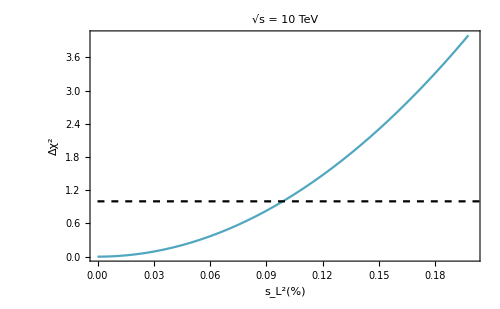

```mathematica
lineplot=ListPlot[{Transpose[{ dyttnew ,intdytchi2enang [dyttnew]}],sig1},Joined->True,PlotStyle->{ColorData[colorselecitonumber][5],{Dashed,Black}},Frame->True,FrameLabel->{Style[DisplayForm["s_L^2(%)"],Black,18,FontFamily->"Times"],Style["Δχ^2",Black,18,FontFamily->"Times"]},
PlotLabel->Style[DisplayForm[SqrtBox["s"] ]  Row[{" = ",10 TeV}]  ,Black,18,FontFamily->"Times"],
PlotRange->{{0,0.2},{0,4}},
FrameTicksStyle->Directive[Black,15],ImageSize->500]
```